```mathematica
Quit[]
```

```mathematica
$Path=Prepend[$Path,NotebookDirectory[]];
<<UpSetChart`
```

```mathematica
sets=UpSetChart`TestData`DummyData[3];
calc = UpSetChart`Calculations`CalcThenSortAndFilter[sets];
```

```mathematica
gc=UpSetChart`Graphics`Utilities`GraphicComponents[calc["sets"], calc["comparisons"]];
```

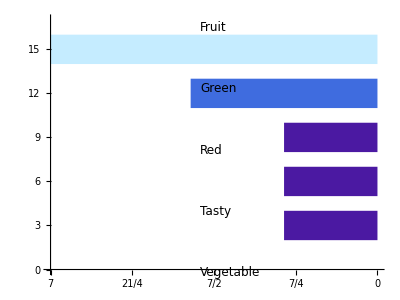

```mathematica
Graphics[{
gc[[1]],
gc[[3]]
}]
```

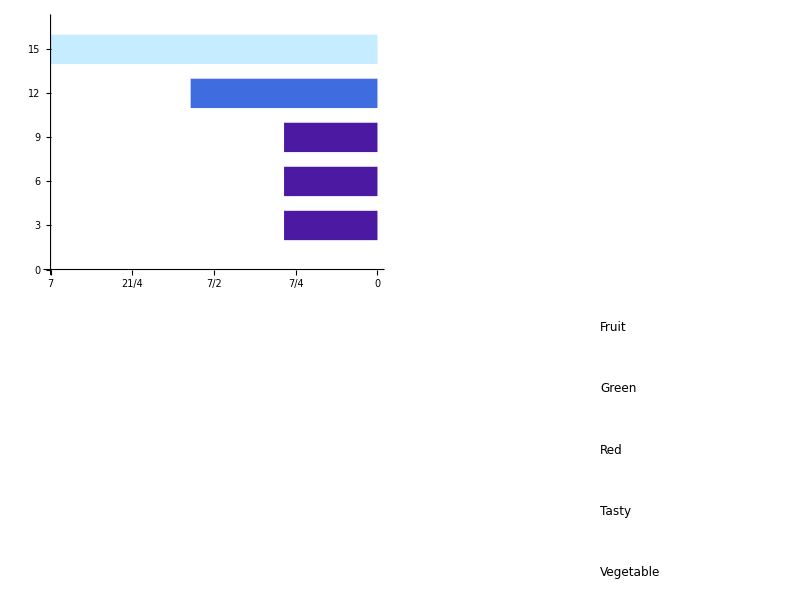

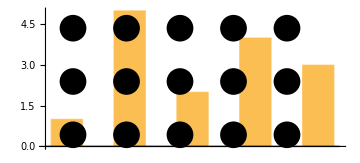

```mathematica
outerBarSpacer=1;
d={1,5,2,4,3};
Graphics[
{

Inset[
BarChart[d,BarSpacing->{1}],
{0,0},
{0,0},
{2Length@d-1+2,Max@d}
],


Inset[
Graphics[Table[
Disk[
{
i+(i-1)+outerBarSpacer-1/2,
j+(j-1)-1/2
},1/2
],{i,Length@d},{j,3}]],

{0,0},
{0,0},
{2Length@d-1,Max@d}
]
},
ImageSize->Medium
]
```

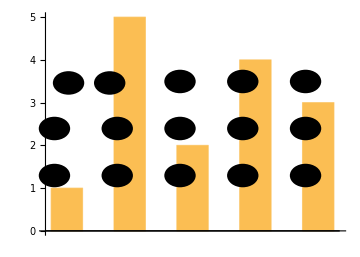

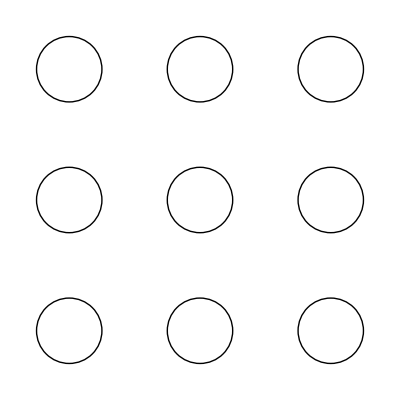

```mathematica
Inset[
BarChart[{1,2,3},BarSpacing->{1},BarOrigin->Right],
{0,0},
{0,4},
{7,3}
],
```

```mathematica
Table[
Disk[
{
i+(i-1)+outerBarSpacer,
j+(j-1)-1/2
},1/2
],{i,3},{j,3}]
```

{{Disk[{2,1/2},1/2],Disk[{2,5/2},1/2],Disk[{2,9/2},1/2]},{Disk[{4,1/2},1/2],Disk[{4,5/2},1/2],Disk[{4,9/2},1/2]},{Disk[{6,1/2},1/2],Disk[{6,5/2},1/2],Disk[{6,9/2},1/2]}}